## Константы

```mathematica
If[True,
A            =- 0.024 (**);
B            = 1.69 (**);
CC          = 0.5 (**);
α            = 10^-5               (* K^-1 *);
T0          = 300                (* K *);
Young   = 1.75 * 10^11 (* Па *);
σf          = 1.1 * 10^8     (* Па *);
ϵf          = 0.000628571;
l            = 10                    (* Длина стержня *);
Tf          =22.2                (* Конечный момент времени *); 
τ            = 0.05                (* Шаг времени *);
a            = 50                    (* Просто константа *);
n            =  10                   (* Число узлов сетки *);
h            = 0.1                  (* Шаг сетки *);
];
```

## Определение всех необходимых функций

```mathematica
F[x_] := a Sin[(π x)/l];
```

```mathematica
T1[x_, t_] := T0 + F[x]t Sin[t];
T2[ x_, t_ ] := T0 + F[x] Cos[2t]Sin[3t];
```

Тепловые деформации

```mathematica
ϵT [T_] := α(T - T0);
```

Полные деформации

```mathematica
ϵ[u_] := D[u, {x, 1}];
```

SetDelayed::write: Tag List in {0.00163083,0.00126933,0.000912268,0.000568453,0.000246346,-0.0000461203,-0.000301745,-0.000514235,-0.000678356,-0.000790068,-0.000846621,-0.000846621,-0.000790068,-0.000678356,-0.000514235,-0.000301745,-0.0000461203,0.000246346,0.000568453,0}[u_] is Protected.

Аналитическое решение (перемещения)

```mathematica
uAnalytical = 
First[Flatten[
DSolve[{
D[D[u[x,t], {x, 1}]-ϵT[T1[x, t]], {x, 1}]== 0,
u[0, t] == 0, 
u[l, t] == 0
},u[x,t],{x, t}]]
]⟦2⟧
```

(5 t Sin[t]-t x Sin[t]-5 t Cos[(π x)/10] Sin[t])/(1000 π)

## Численное решение (метод конечных разностей)

```mathematica
f= D[ϵT[T1[x, t]], {x, 1}]
```

(π t Cos[(π x)/10] Sin[t])/20000

Проверки для шага и количества точек (можем выставлять и то, и то)

```mathematica
If[NumberQ[n],
h = l/n, 
If[NumberQ[h],n = IntegerPart[l/h]; h = l/n]
];
```

Составляем разностное уравнение

```mathematica
(d^2 u)/dx^2== f;
```

```mathematica
(Subscript[u, i+1] - 2 Subscript[u, i] + Subscript[u, i-1])/h^2 == f
```

u_19-2 u_20+u_21==(π t Cos[(π x)/10] Sin[t])/20000

Создаем массив точек и значений функции f в них, далее решаем СЛАУ: Au = F(f(x_1), ..., f(x_n) ). В идеале прогонкой

```mathematica
points = Table[i*h, {i, 0, n}];
```

```mathematica
values = {0}~Join~Table[f/.{ x-> points⟦i⟧}, {i, 1, n-1}]~Join~{0} ;
```

```mathematica
H = Table[
Table[
If [i == j, 
If[i == 0 || i== n, 1,-2/h^2],
If[(i == j-1 || i== j+1)&&j≠ 0 && j≠ n , 1/h^2, 0 ]
]
, {i, 0, n}],
{j, 0, n}
];
```

```mathematica
H // MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | -2 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | -2 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | -2 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | -2 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -2 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -2 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

Численно найденные значения перемещений путем решения ДУ

```mathematica
uNumerical =LinearSolve[H, values] ;
```

Нахождение деформаций (du/dx)

```mathematica
duNumerical = Table[(uNumerical⟦i+1⟧ - uNumerical⟦i⟧)/h, {i, 1, n}] ;
```

## Решение на каждом временном слое

```mathematica
σ = Table[0,{i, 1, n}];
σfv = Table[σf,{i, 1, n}];
ϵ = Table[0,{i, 1, n}]; 
ϵe = Table[0,{i, 1, n}]; 
ϵcrk = Table[0,{i, 1, n}];
T = Table[0,{i, 1, n}];
```

```mathematica
data = {};
For[tt = 0, tt <= Tf, tt = tt+τ,
temp = {};
For [i = 1, i< n, ++i,
T⟦i⟧ = T1[points⟦i⟧, tt] /. t-> tt; 
ϵ⟦i⟧ = duNumerical⟦i⟧ /. t-> tt;
ϵe⟦i⟧ = ϵ⟦i⟧ - ϵT[T⟦i⟧] - ϵcrk⟦i⟧ /. t-> tt;
If[Young*ϵe⟦i⟧<σfv⟦i⟧,
σ⟦i⟧ = Young*ϵe⟦i⟧,
σfv⟦i⟧ = σf(A + B ⅇ^(-CC  * (ϵ⟦i⟧ - ϵT[T⟦i⟧])/ϵf)); σ⟦i⟧ = σfv⟦i⟧; ϵcrk⟦i⟧ = ϵ⟦i⟧ -  ϵT[T⟦i⟧] - σ⟦i⟧/Young; ϵe⟦i⟧ = (First@Flatten@Solve[σf(A + B ⅇ^(-CC*(x +ϵcrk⟦i⟧)/ϵf))== σfv⟦i⟧, x])⟦2⟧;
];
AppendTo[temp, {tt, T⟦i⟧, σ⟦i⟧, ϵ⟦i⟧, ϵ⟦i⟧ -  ϵT[T⟦i⟧], ϵcrk⟦i⟧}]
];
AppendTo[data, temp]
];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

## Картиночки

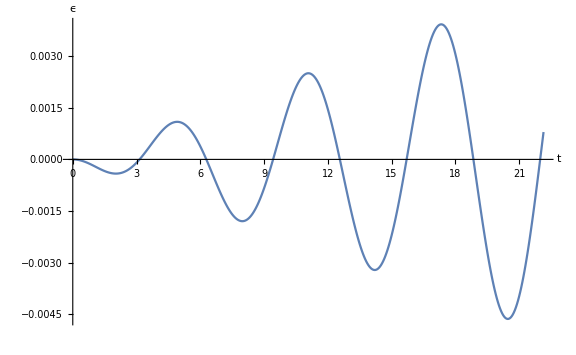

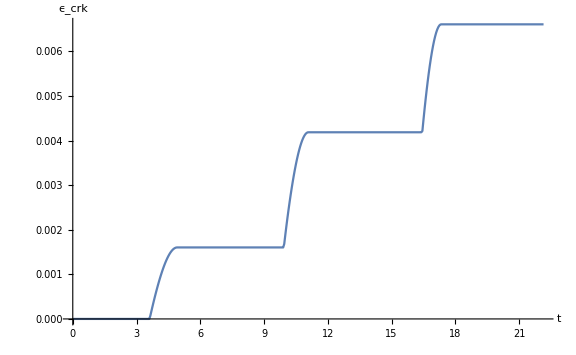

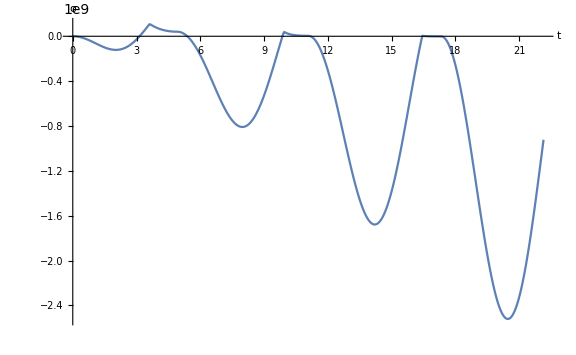

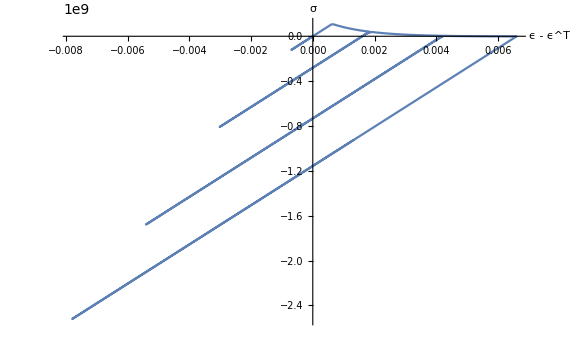

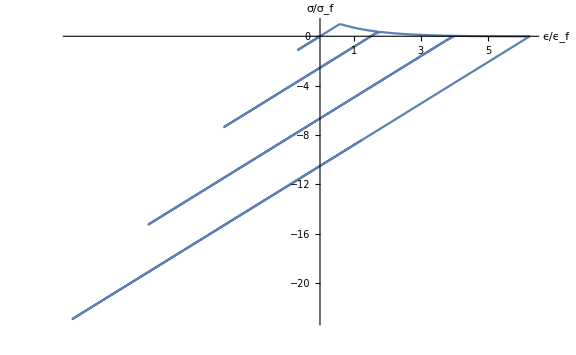

-Graphics-

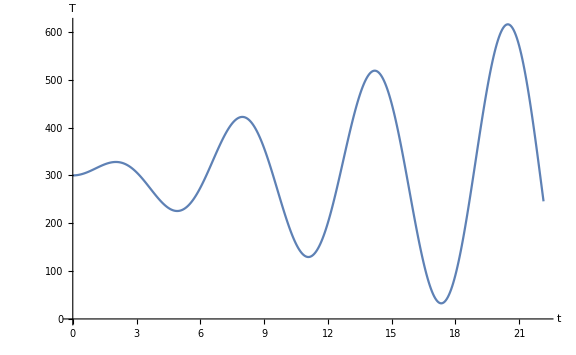

```mathematica
ListPlot[Table[{data⟦i, 2, 1⟧, data⟦i, 2, 4⟧}, {i, 1,IntegerPart@ (Tf/τ)}], Joined->True,ImageSize->Large, AxesLabel->{"t", "ϵ"}]
ListPlot[Table[{data⟦i, 2, 1⟧, data⟦i, 2, -1⟧}, {i, 1,IntegerPart@ (Tf/τ)}], Joined->True,ImageSize->Large,  AxesLabel->{"t", "ϵ_crk"}]
ListPlot[Table[{data⟦i, 2, 1⟧, data⟦i, 2, 3⟧}, {i, 1,IntegerPart@ (Tf/τ)}], Joined->True,ImageSize->Large,  AxesLabel->{"t", "σ"}]
ListPlot[Table[{data⟦i, 2, 5⟧, data⟦i, 2, 3⟧}, {i, 1,IntegerPart@ (Tf/τ)}], Joined->True, ImageSize->Large,AxesLabel->{"ϵ - ϵ^T", "σ"}]
ListPlot[Table[{data⟦i, 2, 4⟧/ϵf, data⟦i, 2, 3⟧/σf}, {i, 1,IntegerPart@ (Tf/τ)}], Joined->True,ImageSize->Large, Ticks->{Table[i,{i,1,10}], Automatic},AxesLabel->{"ϵ/ϵ_f", "σ/σ_f"}]
ListPlot[Table[{data⟦i, 2, 1⟧, data⟦i, 2, 4⟧}, {i, 1,IntegerPart@ (Tf/τ)}], Joined->True,ImageSize->Large, AxesLabel->{"t", "ϵ"}]
ListPlot[Table[{data⟦i, 2, 1⟧, data⟦i, 2, 2⟧}, {i, 1,IntegerPart@ (Tf/τ)}], Joined->True, ImageSize->Large,AxesLabel->{"t", "T"}]
```